### QCD 1 - loop example: gluon self energy

```mathematica
$LoadTARCER=True;
```

```mathematica
<<HighEnergyPhysics`FeynCalc`
```

Loading FeynCalc from /home/rolfm/HighEnergyPhysics

Loading TARCER /home/rolfm/HighEnergyPhysics/Tarcer/tarcerLinuxx8664bit25.mx

FeynCalc 8.1.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.4 patched for use with FeynCalc

#### The graphs

This generates the 1-loop self energy diagrams using a model file for QCD from the Models directory in HighEnergyPhyiscs.

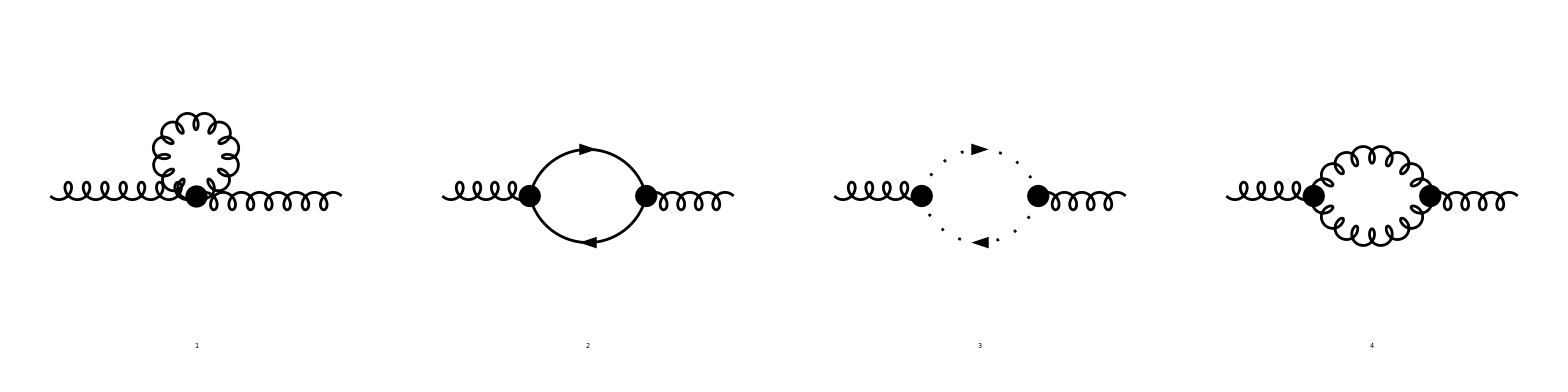

```mathematica
Paint[inserts=InsertFields[CreateTopologies[1,1->1,ExcludeTopologies->Tadpoles],{V[5]}->{V[5]},InsertionLevel->{Classes},GenericModel->"FCQCDLorentz",Model->"FCQCD"],ColumnsXRows->{4,1},SheetHeader->None,Numbering->Simple];
```

Inserting the analytical expressions. The momentum flowing into the loop is p, since the outgoing momentum is k1 and by definition from the Model file p1+k1=0 we have to replace k1 by -p. The loop momentum is q and the Lorentz indices of the external gluons are μ and ν.

```mathematica
amps= CreateFeynAmp[inserts,Truncated->True,PreFactor->1,AmplitudeLevel->{Classes}]/.{p1:>p,q1:>q,li1:>μ,li2:>ν}/.FeynAmpList[__]:>List /. FeynAmp[_,_,x_]:>x;
```

#### Calculating the bare 2-loop on-shell gluon selfenergy diagrams

```mathematica
TableForm[amps]
```

1/2 Π_g^li3li4(q) V_ci1ci2ci4ci4^μνli3li4(p, -p, -q, q)
-tr(2 Tf N_f Π_q(q).T_ci2.Q^ν.Π_q(q-p).T_ci1.Q^μ)
-Π_u(q) (Λ̃)^ν(q) f_ci5ci3ci1 f_ci3ci5ci2 Π_u(q-p) (Λ̃)^μ(q-p)
1/2 f_ci1ci4ci6 f_ci2ci4ci6 Π_g^li3li4(q) Π_g^li5li6(p-q) V^μli3li5(p, -q, q-p) V^νli4li6(-p, q, p-q)

We recognize the combinatorical factors and minus signs provided by FeynArts.

### The ghost loop

Explicitly inserting the Feynman rules for a general gauge and summing the amplitudes.

```mathematica
gh1 =amps[[3]]
```

-Π_u(q) (Λ̃)^ν(q) f_ci5ci3ci1 f_ci3ci5ci2 Π_u(q-p) (Λ̃)^μ(q-p)

```mathematica
gh2=SUNSimplify[Explicit[gh1,Dimension->D]]
```

-(C_A g_s^2 q^ν δ_ci1ci2 (q^μ-p^μ))/(q^2 (q-p)^2)

```mathematica
gh3=Collect2[Contract[gh2],ξ]/.CA->1/.Gstrong->1/.SUNDelta[__]:>1
```

(p^μ q^ν)/(q^2 (q-p)^2)-(q^μ q^ν)/(q^2 (q-p)^2)

Do a tensor integral decomposition by using the function TID.

```mathematica
gh4=TID[gh3,q]
```

(q^2 (g^μν/(1-D)-(p^μ p^ν)/((1-D) p^2)))/(q^2.(q-p)^2)+((p·q)^2 ((D p^μ p^ν)/((1-D) (p^2)^2)-g^μν/((1-D) p^2)))/(q^2.(q-p)^2)+(p^μ p^ν p·q)/(p^2 q^2.(q-p)^2)

```mathematica
?ToFI
```

ToFI[expr, {q1, q2}, {p}] translates all non-tensorial 
loop integrals in expr into TFI notation from Tarcer. 
ToFI[expr, {q}, {p}] introduces TBI B0-like integrals. ToFI can be extended to more external particles and more loops if needed.

```mathematica
ghostloop=ToFI[gh4,{q},{p}]//Factor2
```

((-D p^μ p^ν-p^2 g^μν+2 p^μ p^ν) B_({1,0}{1,0})^(D))/(4 (1-D))

```mathematica
%//InputForm
```

((2*FVD[p, μ]*FVD[p, ν] - D*FVD[p, μ]*FVD[p, ν] - MTD[μ, ν]*SPD[p, p])*
  TBI[D, SPD[p, p], {{1, 0}, {1, 0}}])/(4*(1 - D))

### The gluon loop

Explicitly inserting the Feynman rules for a general gauge and summing the amplitudes.

```mathematica
gl1 =amps[[4]]
```

1/2 f_ci1ci4ci6 f_ci2ci4ci6 Π_g^li3li4(q) Π_g^li5li6(p-q) V^μli3li5(p, -q, q-p) V^νli4li6(-p, q, p-q)

```mathematica
gl2=SUNSimplify[Explicit[gl1,Gauge->1-ξ,Dimension->D]]
```

-1/(2 q^2 (p-q)^2)C_A g_s^2 δ_ci1ci2 ((ξ q^li3 q^li4)/q^2-g^li3li4) (g^li5μ (q^li3-2 p^li3)+g^li3μ (p^li5+q^li5)+g^li3li5 (p^μ-2 q^μ)) (g^li6ν (2 p^li4-q^li4)+g^li4ν (-p^li6-q^li6)+g^li4li6 (2 q^ν-p^ν)) ((ξ (p^li5-q^li5) (p^li6-q^li6))/(p-q)^2-g^li5li6)

```mathematica
gl3=Collect2[Contract[gl2],ξ]/.CA->1/.Gstrong->1/.SUNDelta[__]:>1
```

1/2 ξ^2 (1/(p-q)^2)^2 (q^μ p^2-p^μ p·q) (q^ν p^2-p^ν p·q) (1/q^2)^2+1/(2 (p-q)^2 q^2)(D p^μ p^ν-6 p^μ p^ν-2 D q^μ p^ν+3 q^μ p^ν-2 D p^μ q^ν+3 p^μ q^ν+4 D q^μ q^ν-6 q^μ q^ν+5 g^μν p^2-2 g^μν p·q+2 g^μν q^2)+1/(2 (p-q)^2 q^2)ξ (-(g^μν (p^2)^2)/(p-q)^2+(p^μ p^ν p^2)/(p-q)^2-(2 q^μ q^ν p^2)/(p-q)^2-(q^μ q^ν p^2)/q^2+(2 g^μν p^2 q^2)/(p-q)^2-(4 g^μν (p·q)^2)/q^2-(g^μν (q^2)^2)/(p-q)^2-(g^μν (q^2)^2)/q^2+(q^μ p^ν p·q)/(p-q)^2+(3 q^μ p^ν p·q)/q^2+(p^μ q^ν p·q)/(p-q)^2+(3 p^μ q^ν p·q)/q^2-(2 q^μ q^ν p·q)/q^2-(2 p^μ p^ν q^2)/(p-q)^2-(p^μ p^ν q^2)/q^2-(q^μ p^ν q^2)/q^2-(p^μ q^ν q^2)/q^2+(q^μ q^ν q^2)/(p-q)^2+(q^μ q^ν q^2)/q^2+(4 g^μν p·q q^2)/q^2)

This is the A_μνin eq. (A.3) from T.Muta's book "Foundation of Quantum Chromodynamics".

```mathematica
Collect2[2 Coefficient[gl3,ξ,0]/.p->(-k)/.FeynAmpDenominator[__]:>1,LorentzIndex,Factoring->False]
```

(D-6) k^μ k^ν+(2 D-3) k^ν q^μ+(2 D-3) k^μ q^ν+(4 D-6) q^μ q^ν+g^μν (2 k·q+5 k^2+2 q^2)

This should be the B_μνin eq. (A.4) from T.Muta's book "Foundation of Quantum Chromodynamics".

```mathematica
bmunu=Collect2[FCI[FCE[FDS[Coefficient[2 gl3,ξ,1],q]/.p->(-k)]],{μ,ν}]
```

-(2 g^μν (2 k·q+q^2)^2)/(q^2.q^2.(k+q)^2)-(2 q^2 k^μ k^ν)/(q^2.q^2.(k+q)^2)-(2 q^μ q^ν (-2 k·q+k^2-q^2))/(q^2.q^2.(k+q)^2)+(2 k^ν q^μ (3 k·q+q^2))/(q^2.q^2.(k+q)^2)+(2 k^μ q^ν (3 k·q+q^2))/(q^2.q^2.(k+q)^2)

However, it is not evident that it is really the same. Therefore we enter eq. (A.4) and subtract it from the above.

```mathematica
mutabmunu1=FAD[q,q+k] .(-FAD[q](SPD[q]+2SPD[k,q])^2MTD[μ,ν] +
FAD[q]FVD[q,ν]FVD[q,μ](SPD[q]+2SPD[k,q]-SPD[k])+
FAD[q](SPD[q]+3SPD[k,q])(FVD[q,μ]FVD[k,ν]+FVD[q,ν]FVD[k,μ])-
FVD[k,μ]FVD[k,ν])
```

1/(([q^2]) ([(k+q)^2])).(g^μν (2 k·q+q^2)^2 (-1/[q^2])+(3 k·q+q^2) (k^ν q^μ+k^μ q^ν) 1/[q^2]+q^μ q^ν (2 k·q-k^2+q^2) 1/[q^2]-k^μ k^ν)

```mathematica
mutabmunu=FCI[mutabmunu1+ (mutabmunu1/.{q:>(q+k),k:>-k})]
```

1/(q^2.(k+q)^2).(-(g^μν (2 k·q+q^2)^2)/q^2-k^μ k^ν+(q^μ q^ν (2 k·q-k^2+q^2))/q^2+((3 k·q+q^2) (k^ν q^μ+k^μ q^ν))/q^2)+1/((k+q)^2.q^2).(-(g^μν ((k+q)^2-2 k·(k+q))^2)/(k+q)^2-k^μ k^ν+(((k+q)^2-3 k·(k+q)) (k^ν (-(k+q)^μ)-k^μ (k+q)^ν))/(k+q)^2+((k+q)^μ (k+q)^ν ((k+q)^2-2 k·(k+q)-k^2))/(k+q)^2)

```mathematica
Collect2[ScalarProductCancel@FeynAmpDenominatorSimplify[Calc[mutabmunu- bmunu],q],q]
```

0

This proves that bmunu is equivalent to (A.4) of T. Muta.

Project out  the C_μνin eq. (A.5) from T.Muta's book.

```mathematica
FCI[FCE[Coefficient[ 2 gl3,ξ,2]/.p->(-k)]/.FAD[q,q,q+k,q+k]:>FAD[q,q+k]]
```

(1/q^2)^2 (1/(-k-q)^2)^2 (k^2 q^μ-k^μ k·q) (k^2 q^ν-k^ν k·q)

```mathematica
gl4=Collect2[FeynAmpDenominatorSimplify[gl3,q],q]
```

(ξ^2 q^μ q^ν (p^2)^2)/(2 q^2.q^2.(q-p)^2.(q-p)^2)+(ξ^2 p^μ p^ν (p·q)^2)/(2 q^2.q^2.(q-p)^2.(q-p)^2)-(ξ^2 q^μ p^ν p^2 p·q)/(2 q^2.q^2.(q-p)^2.(q-p)^2)-(ξ^2 p^μ q^ν p^2 p·q)/(2 q^2.q^2.(q-p)^2.(q-p)^2)-(4 ξ g^μν (p·q)^2)/(q^2.q^2.(q-p)^2)-(ξ g^μν (q^2)^2)/(q^2.q^2.(q-p)^2)-(ξ q^μ q^ν p^2)/(q^2.q^2.(q-p)^2)+(3 ξ q^μ p^ν p·q)/(q^2.q^2.(q-p)^2)+(3 ξ p^μ q^ν p·q)/(q^2.q^2.(q-p)^2)-(2 ξ q^μ q^ν p·q)/(q^2.q^2.(q-p)^2)-(ξ p^μ p^ν q^2)/(q^2.q^2.(q-p)^2)-(ξ q^μ p^ν q^2)/(q^2.q^2.(q-p)^2)-(ξ p^μ q^ν q^2)/(q^2.q^2.(q-p)^2)+(ξ q^μ q^ν q^2)/(q^2.q^2.(q-p)^2)+(4 ξ g^μν p·q q^2)/(q^2.q^2.(q-p)^2)-((2 D-3) q^μ p^ν)/(2 q^2.(q-p)^2)-((2 D-3) p^μ q^ν)/(2 q^2.(q-p)^2)+((2 D-3) q^μ q^ν)/(q^2.(q-p)^2)+(D p^μ p^ν-6 p^μ p^ν+5 g^μν p^2)/(2 q^2.(q-p)^2)-(g^μν p·q)/(q^2.(q-p)^2)+(g^μν q^2)/(q^2.(q-p)^2)

```mathematica
?TID
```

TID[amp, q] does a 1-loop tensor integral decomposition, transforming the
Lorentz indices away from the integration momentum q.

```mathematica
gl4[[1]]
```

-((2 D-3) p^ν q^μ)/(2 q^2.(q-p)^2)

```mathematica
gl4//Length
```

21

```mathematica
gl4[[11]]//FCE//InputForm
```

-(ξ^2*FAD[q, q, -p + q, -p + q]*FVD[p, ν]*FVD[q, μ]*SPD[p, p]*SPD[p, q])/2

```mathematica
gl5=Collect2[TID[gl4,q],q]
```

-(2 ξ (D p^μ p^ν-g^μν p^2) (p·q)^3)/((D-1) q^2.q^2.(q-p)^2 (p^2)^2)+(ξ^2 (p^μ p^ν-g^μν p^2) (p·q)^2)/(2 (D-1) q^2.q^2.(q-p)^2.(q-p)^2)+((2 D-3) (D p^μ p^ν-g^μν p^2) (p·q)^2)/((D-1) q^2.(q-p)^2 (p^2)^2)-(ξ (-5 D p^μ p^ν+6 p^μ p^ν+4 D g^μν p^2-5 g^μν p^2) (p·q)^2)/((D-1) q^2.q^2.(q-p)^2 p^2)+(ξ (D p^μ p^ν-g^μν p^2) (p·q)^2 q^2)/((D-1) q^2.q^2.(q-p)^2 (p^2)^2)-((2 D p^μ p^ν-3 p^μ p^ν+g^μν p^2) p·q)/(q^2.(q-p)^2 p^2)+(2 ξ (-D p^μ p^ν+2 p^μ p^ν+2 D g^μν p^2-3 g^μν p^2) p·q q^2)/((D-1) q^2.q^2.(q-p)^2 p^2)-(ξ (p^μ p^ν+D g^μν p^2-2 g^μν p^2) (q^2)^2)/((D-1) q^2.q^2.(q-p)^2 p^2)+(D p^μ p^ν-6 p^μ p^ν+5 g^μν p^2)/(2 q^2.(q-p)^2)-(ξ^2 p^2 (p^μ p^ν-g^μν p^2) q^2)/(2 (D-1) q^2.q^2.(q-p)^2.(q-p)^2)-(ξ (D p^μ p^ν-2 p^μ p^ν+g^μν p^2) q^2)/((D-1) q^2.q^2.(q-p)^2)+((-2 D p^μ p^ν+3 p^μ p^ν+3 D g^μν p^2-4 g^μν p^2) q^2)/((D-1) q^2.(q-p)^2 p^2)

```mathematica
gl6=ToFI[gl5,{q},{p}]//FCE//Factor2
```

-1/(8 (1-D))(-ξ^2 p^6 g^μν B_({2,0}{2,0})^(D)+4 ξ^2 p^4 g^μν B_({2,0}{1,0})^(D)+2 ξ^2 p^2 g^μν B_({1,0}{1,0})^(D)-8 D ξ p^4 g^μν B_({2,0}{1,0})^(D)+12 ξ p^4 g^μν B_({2,0}{1,0})^(D)-8 ξ p^2 g^μν B_({1,0}{1,0})^(D)+12 D p^2 g^μν B_({1,0}{1,0})^(D)-10 p^2 g^μν B_({1,0}{1,0})^(D)+ξ^2 p^4 p^μ p^ν B_({2,0}{2,0})^(D)-4 ξ^2 p^2 p^μ p^ν B_({2,0}{1,0})^(D)-2 ξ^2 p^μ p^ν B_({1,0}{1,0})^(D)+8 D ξ p^2 p^μ p^ν B_({2,0}{1,0})^(D)-12 ξ p^2 p^μ p^ν B_({2,0}{1,0})^(D)+8 ξ p^μ p^ν B_({1,0}{1,0})^(D)-14 D p^μ p^ν B_({1,0}{1,0})^(D)+12 p^μ p^ν B_({1,0}{1,0})^(D))

```mathematica
gluonloop=Collect2[TarcerRecurse[gl6],{μ,ν}]/.a_Plus:>Collect2[a,ξ]/;FreeQ[a,TBI]
```

(((D-4) (D-1) ξ^2-4 (D-1) (2 D-7) ξ-2 (7 D-6)) p^μ p^ν B_({1,0}{1,0})^(D))/(8 (D-1))-(p^2 ((D-4) (D-1) ξ^2-4 (D-1) (2 D-7) ξ-2 (6 D-5)) g^μν B_({1,0}{1,0})^(D))/(8 (D-1))

Only by adding the ghost contribution transversality is restored.

```mathematica
nonfermionicresult=Factor2[gluonloop+ghostloop]/.h_Plus:>Collect2[h,ξ]
```

-(((D-4) (D-1) ξ^2-4 (D-1) (2 D-7) ξ-4 (3 D-2)) (p^μ p^ν-p^2 g^μν) B_({1,0}{1,0})^(D))/(8 (1-D))

```mathematica
Contract[FVD[p,μ] nonfermionicresult]
```

0

### The fermion loop

Explicitly inserting the Feynman rules for a general gauge and summing the amplitudes.

```mathematica
fl1=amps⟦2⟧
```

-tr(2 Tf N_f Π_q(q).T_ci2.Q^ν.Π_q(q-p).T_ci1.Q^μ)

Replace the "QuarkMass" variable from the FCQCDLorentz Model file by "M".

```mathematica
fl2=SUNSimplify[Explicit[fl1,Dimension->D]]/.QuarkMass -> M
```

-(Tf N_f g_s^2 δ_ci1ci2 tr((M+γ·q).γ^ν.(M-γ·(p-q)).γ^μ))/((q^2-M^2).((q-p)^2-M^2))

```mathematica
fl3=Contract[fl2/.DiracTrace->TR]/.CA->1/.Gstrong->1/.SUNDelta[__]:>1
```

-(4 M^2 Tf N_f g^μν)/((q^2-M^2).((q-p)^2-M^2))+(4 q^2 Tf N_f g^μν)/((q^2-M^2).((q-p)^2-M^2))-(4 Tf N_f g^μν p·q)/((q^2-M^2).((q-p)^2-M^2))+(4 Tf N_f p^ν q^μ)/((q^2-M^2).((q-p)^2-M^2))+(4 Tf N_f p^μ q^ν)/((q^2-M^2).((q-p)^2-M^2))-(8 Tf N_f q^μ q^ν)/((q^2-M^2).((q-p)^2-M^2))

```mathematica
fl4=Collect2[TID[fl3,q],q]
```

(4 q^2 Tf N_f (D p^2 g^μν-3 p^2 g^μν+2 p^μ p^ν))/((D-1) p^2 (q^2-M^2).((q-p)^2-M^2))-(8 Tf N_f (p·q)^2 (D p^μ p^ν-p^2 g^μν))/((D-1) (p^2)^2 (q^2-M^2).((q-p)^2-M^2))-(4 M^2 Tf N_f g^μν)/((q^2-M^2).((q-p)^2-M^2))-(4 Tf N_f p·q (p^2 g^μν-2 p^μ p^ν))/(p^2 (q^2-M^2).((q-p)^2-M^2))

```mathematica
cc=Collect2[SPC[SPC[fl4,q,FDS->True],q,FDS->True],q]
```

(4 (D-2) Tf N_f (p^2 g^μν-p^μ p^ν))/((D-1) p^2 (q^2-M^2))-(2 Tf N_f (D p^2+4 M^2-2 p^2) (p^2 g^μν-p^μ p^ν))/((D-1) p^2 (q^2-M^2).((q-p)^2-M^2))

```mathematica
fermionloop=Factor2[ToTFI[fl4,q,p]]
```

-(2 Tf N_f (p^μ p^ν-p^2 g^μν) (-2 D A_{1,M}^(D)+4 A_{1,M}^(D)+4 M^2 B_({1,M}{1,M})^(D)+D p^2 B_({1,M}{1,M})^(D)-2 p^2 B_({1,M}{1,M})^(D)))/((1-D) p^2)

```mathematica
TimeUsed[]
```

5.77236